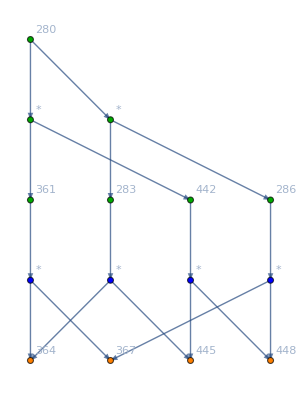

```mathematica
Graph[DependencyGraph[allGraphs,280],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->Table[k->Labeled[allGraphs[k,"graph"],Style[k,Bold]],{k,{280,283,364,445,286,367,448,361,442}}]]
```

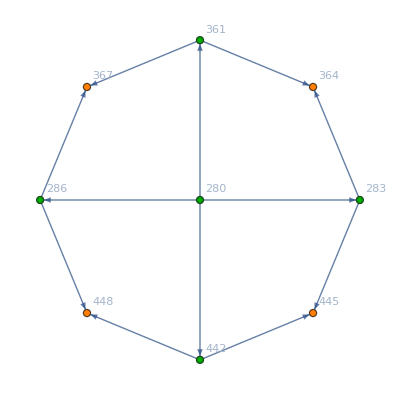

```mathematica
Graph[Join[{280->361,280->442,280->283,280->286},Problems[allGraphs,0]],
GraphLayout->"TutteEmbedding",
VertexLabels->Table[k->Labeled[allGraphs[k,"graph"],Style[k,Bold]],{k,{280,283,364,445,286,367,448,361,442}}],
VertexStyle->Table[k->ColourForKey[allGraphs,k],{k,{280,283,364,445,286,367,448,361,442}}]]
```